```mathematica
FusionAtlasPaths={"~/projects/fusionatlas/package/"};
$Path=$Path~Join~FusionAtlasPaths;
<<FusionAtlas`
```

Loading FusionAtlas` version 0
Read more at http://tqft.net/wiki/Atlas_of_subfactors

Found precomputed data in /Users/scott/projects/fusionatlas/data

```mathematica
δ=N[DimensionOfGenerator[g=GraphFromString["gbg1v1v1v1p1v1x0p1x0v0x0p1x0"]]]
```

2.11199

```mathematica
estimates={1.898828922115942,2.1058754866365414,2.1109238674071036,2.1117437579597294,2.111929587258651,2.111975381548851,2.1119868696969983,2.111989762044646,2.1119904907663902,2.1119906743925476}
```

{1.89883,2.10588,2.11092,2.11174,2.11193,2.11198,2.11199,2.11199,2.11199,2.11199}

```mathematica
Solve[{d-x==a1,d-x/r==a2,d-x/r^2==a3},{d,x,r}]
```

{{x→(-a1^2+2 a1 a2-a2^2)/(a1-2 a2+a3),d→(-a2^2+a1 a3)/(a1-2 a2+a3),r→(a1-a2)/(a2-a3)}}

```mathematica
fancy=Table[(estimates⟦i⟧estimates⟦i+2⟧-estimates⟦i+1⟧^2)/(estimates⟦i⟧-2estimates⟦i+1⟧+estimates⟦i+2⟧),{i,1,Length[estimates]-2}]
```

{2.11105,2.1119,2.11198,2.11199,2.11199,2.11199,2.11199,2.11199}

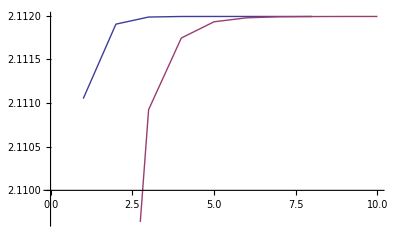

```mathematica
ListPlot[{fancy,estimates},PlotJoined->True]
```

```mathematica
δ-estimates
```

{0.213162,0.00611525,0.00106687,0.000246978,0.000061149,0.0000153547,3.86656×10^-6,9.74208×10^-7,2.45487×10^-7,6.18605×10^-8}

```mathematica
Most[%]/Rest[%]
```

{34.8574,5.73196,4.31969,4.03896,3.98243,3.97116,3.96892,3.96848,3.96839}

```mathematica
d^2
```

4.61803

```mathematica
Log[%]
```

{-1.75029,-4.94054,-7.43464,-9.2632,-10.7103,-12.0577,-13.386,-14.7108,-16.035,-17.3591}

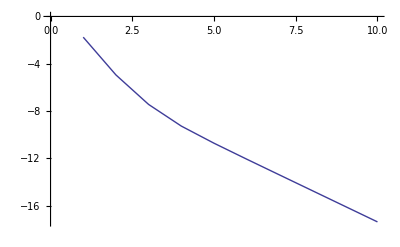

```mathematica
ListPlot[%,PlotJoined->True]
```